```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/github/Smoldyn/examples/S8_reactions/bounce

```mathematica
(* Set parameters for radial distribution function comparison.
maxradius is rdf maximum radius.
nmolec comes from the Smoldyn file.
volume comes from the Smoldyn file.
radius is the molecule radius *)
maxradius=20
nmolec=6112
volume=1000000
radius=2.5
```

20

6112

1000000

2.5

```mathematica
(* This is the radial distribution function for hard spheres.
h is the fractional volume occupancy.
x is the radius input, scaled relative to the molecule diameter. *)
changfunction[h_,x_]:=Module[{Avalue,Bvalue,Cvalue,zd,zs,yplus,yminus,f,a1,a2,a3,b1,b2,b3,b4,b5,b6,c1,c2,c3,c4,c5,c6,c7,c8,c9,H1,H2,H3,g},
Avalue=(-2*h+zd)/(1-h);
Bvalue=(-2h-zd/2)/(1-h);
Cvalue=Sqrt[3]*zs/(2*(1-h));
zd=yplus-yminus;
zs=yplus+yminus;
yplus=(2*h*f)^(1/3)*(Sqrt[2*h^4/f^2+1]+1)^(1/3);
yminus=(2*h*f)^(1/3)*(Sqrt[2*h^4/f^2+1]-1)^(1/3);
f=3+3*h-h^2;
a1=(-2*h*(1-h-3*h^2)+(1-3*h-4*h^2)*zd+(1+h/2)*zd^2)/(3*(2*h^2+zd^2)*(1-h)^2);
a2=(h*(2+4*h-3*h^2)-(1-3*h-4*h^2)*zd+2*(1+h/2)*zd^2)/(3*(2*h^2+zd^2)*(1-h)^2);
a3=((1-3*h-4*h^2)*(4*h^2+zd^2)+h*(2-5*h^2)*zd)/(Sqrt[3]*zs*(2*h^2+zd^2)*(1-h)^2);
b1=-4/3*h*((2*h^2-zd^2)*(1-6*h-3*h^2+20*h^3+15*h^4)+zd*h*(16+24*h-21*h^2-13*h^3+21*h^4))/((2*h^2+zd^2)^3*(1-h)^2);
b2=-b1;
b3=8*Sqrt[3]*h^2*((4*h^2+zd^2)*(2-10*h-24*h^2+30*h^3+79*h^4+21*h^5-17*h^6)+2*zd*h*(16+40*h-h^2-50*h^3+11*h^4+52*h^5+13*h^6))/(zs^3*(2*h^2+zd^2)^3*(1-h)^2);
b4=-2/3*h*(2*h*(10+28*h+21*h^2-13*h^3-19*h^4)+zd*(2-12*h-18*h^2+28*h^3+27*h^4)+zd^2*(4-6*h-18*h^2-7*h^3))/((2*h^2+zd^2)^2*(1-h)^3);
b5=-4/3*h^2*(4*(6-30*h-82*h^2+58*h^3+222*h^4+94*h^5-25*h^6)-zd*(24-10*h-164*h^2-156*h^3+22*h^4+41*h^5)-zd^2*(10+32*h+15*h^2-31*h^3-26*h^4))/(zs^2*(2*h^2+zd^2)^2*(1-h)^3);
b6=4/Sqrt[3]*h^2*(24-10*h-164*h^2-156*h^3+22*h^4+41*h^5-zd*(10+32*h+15*h^2-31*h^3-26*h^4))/(zs*(2*h^2+zd^2)^2*(1-h)^3);
c1=-32*h^3*((2*h^2-zd^2)*(4-56*h-136*h^2+130*h^3+343*h^4-268*h^5-665*h^6-170*h^7+89*h^8)+zd*h*(92+116*h-744*h^2-1468*h^3+332*h^4+1902*h^5+251*h^6-925*h^7-285*h^8))/(zs^2*(2*h^2+zd^2)^5*(1-h)^2);
c2=-c1;
c3=64*Sqrt[3]*h^4*((4*h^2+zd^2)*(24-312*h-1252*h^2-40*h^3+3854*h^4+1658*h^5-6616*h^6-6376*h^7+593*h^8+1799*h^9+107*h^10)+2*zd*h*(276+624*h-1960*h^2-6976*h^3-3208*h^4+8690*h^5+7499*h^6-4996*h^7-6541*h^8-610*h^9+641*h^10))/(zs^5*(2*h^2+zd^2)^5*(1-h)^2);
c4=-8/3*h^2*(2*h*(36-92*h-360*h^2+156*h^3+982*h^4+747*h^5+195*h^6+37*h^7)-3*zd*h*(4+8*h-94*h^2-60*h^3+280*h^4+256*h^5+11*h^6)+zd^2*(4-60*h-84*h^2+190*h^3+150*h^4-258*h^5-185*h^6))/((2*h^2+zd^2)^4*(1-h)^3);
c5=-32*h^4*(96-1248*h-4960*h^2-256*h^3+14976*h^4+7232*h^5-24376*h^6-25632*h^7-724*h^8+5348*h^9+384*h^10-zd*(72-96*h-1152*h^2-932*h^3+3012*h^4+4920*h^5+604*h^6-2286*h^7-708*h^8+211*h^9)+zd^2*(12-24*h-110*h^2+150*h^3+522*h^4-32*h^5-774*h^6-462*h^7-11*h^8))/(zs^4*(2*h^2+zd^2)^4*(1-h)^3);
c6=32*Sqrt[3]*h^4*(72-96*h-1152*h^2-932*h^3+3012*h^4+4920*h^5+604*h^6-2286*h^7-708*h^8+211*h^9+zd*(12-24*h-110*h^2+150*h^3+522*h^4-32*h^5-774*h^6-462*h^7-11*h^8))/(zs^3*(2*h^2+zd^2)^4*(1-h)^3);
c7=2/3*h^2*(4*h*(34+18*h-195*h^2-332*h^3-144*h^4+69*h^5+64*h^6)+2*zd*(2+6*h+30*h^2+176*h^3+174*h^4-66*h^5-79*h^6)+3*zd^2*(4-14*h-32*h^2+32*h^3+68*h^4+23*h^5))/((2*h^2+zd^2)^3*(1-h)^4);
c8=-8/3*h^3*(12+48*h+280*h^2+1224*h^3+1776*h^4-80*h^5-1794*h^6-816*h^7+79*h^8+zd*(36-88*h-420*h^2+72*h^3+1172*h^4+897*h^5-63*h^6-148*h^7)-zd^2*(68+48*h-432*h^2-760*h^3-192*h^4+342*h^5+197*h^6))/(zs^2*(2*h^2+zd^2)^3*(1-h)^4);
c9=8/3*Sqrt[3]*h^3*((4*h^2+zd^2)*(36-88*h-420*h^2+72*h^3+1172*h^4+897*h^5-63*h^6-148*h^7)-zd*(12+48*h+416*h^2+1320*h^3+912*h^4-1600*h^5-2178*h^6-132*h^7+473*h^8))/(zs^3*(2*h^2+zd^2)^3*(1-h)^4);
H1=a1*Exp[Avalue*(x-1)]+a2*Exp[Bvalue*(x-1)]*Cos[Cvalue*(x-1)]+a3*Exp[Bvalue*(x-1)]*Sin[Cvalue*(x-1)];
H2=b1*Exp[Avalue*(x-2)]+
b2*Exp[Bvalue*(x-2)]*Cos[Cvalue*(x-2)]+
b3*Exp[Bvalue*(x-2)]*Sin[Cvalue*(x-2)]+
b4*(x-2)*Exp[Avalue*(x-2)]+
b5*(x-2)*Exp[Bvalue*(x-2)]*Cos[Cvalue*(x-2)]+b6*(x-2)*Exp[Bvalue*(x-2)]*Sin[Cvalue*(x-2)];
H3=c1*Exp[Avalue*(x-3)]+
c2*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c3*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)]+
c4*(x-3)*Exp[Avalue*(x-3)]+
c5*(x-3)*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c6*(x-3)*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)]+
c7*(x-3)^2*Exp[Avalue*(x-3)]+
c8*(x-3)^2*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c9*(x-3)^2*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)];
g=1/x*(HeavisideTheta[x-1]*H1+HeavisideTheta[x-2]*H2+HeavisideTheta[x-3]*H3);
g]
```

```mathematica
(* Average molecule density *)
avdensity=N[nmolec/volume]
```

0.006112

```mathematica
(* Simulation data *)
simdata=Import["crowding3Dout.txt","CSV"];
(* Remove the time value and one level of nesting *)
simdata1=Drop[simdata[[1]],1];
(* Scale relative to average density *)
simdata2=simdata1/avdensity
```

{0.,0.,0.,0.,0.,0.,0.00188701,0.000472682,0.,0.000589544,0.000724015,0.000804867,0.000681306,0.000292076,0.000126598,0.000553974,0.000586656,0.000782315,0.000933395,0.000840137,0.00139368,0.00247655,0.0048382,0.0357232,0.274733,3.15785,2.85008,2.33164,1.92217,1.61752,1.3923,1.20681,1.07566,0.974468,0.876813,0.823212,0.788578,0.754714,0.744151,0.737857,0.742664,0.754103,0.786846,0.818657,0.876576,0.926944,0.987313,1.03597,1.08625,1.13906,1.18507,1.19767,1.18798,1.15206,1.11645,1.0834,1.04392,1.01317,0.986607,0.964704,0.944521,0.93535,0.925182,0.925144,0.928118,0.937924,0.947601,0.964056,0.975898,0.99412,1.0068,1.02231,1.03554,1.04061,1.04724,1.04506,1.04836,1.03862,1.03147,1.02568,1.01433,1.00299,0.998806,0.991273,0.986024,0.979213,0.982808,0.978032,0.983676,0.983459,0.988729,0.991168,0.99474,1.00449,1.00425,1.00781,1.01321,1.01492,1.01612,1.01327}

```mathematica
(* Create x vector *)
nbin=Length[simdata2]
binwidth=N[maxradius/nbin]
xvector=Table[i,{i,binwidth/2,maxradius-binwidth/2,binwidth}]
```

100

0.2

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9,5.1,5.3,5.5,5.7,5.9,6.1,6.3,6.5,6.7,6.9,7.1,7.3,7.5,7.7,7.9,8.1,8.3,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9,11.1,11.3,11.5,11.7,11.9,12.1,12.3,12.5,12.7,12.9,13.1,13.3,13.5,13.7,13.9,14.1,14.3,14.5,14.7,14.9,15.1,15.3,15.5,15.7,15.9,16.1,16.3,16.5,16.7,16.9,17.1,17.3,17.5,17.7,17.9,18.1,18.3,18.5,18.7,18.9,19.1,19.3,19.5,19.7,19.9}

```mathematica
(* Combine x and y to create plottable simulation data *)
simdata2xy=Transpose[{xvector,simdata2}];
(* Fractional volume occupancy *)
h=4/3*Pi*radius^3*avdensity
```

0.400029

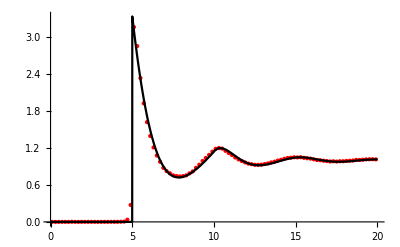

```mathematica
(* Image saved as crowding3rdf.png *)
Show[{ListPlot[simdata2xy,PlotStyle->Directive[Red,PointSize[Medium]]],Plot[changfunction[h,x/(2*radius)],{x,0,4*(2*radius)},PlotStyle->Black,Exclusions->None]},PlotRange->All,AxesStyle->Directive[Bold,12]]
```

```mathematica
(* Compute the rms error for the radial distribution function *)
diff=Table[simdata2[[i]]-changfunction[h,xvector[[i]]/(2*radius)],{i,Length[simdata2]}];
rdferror=Sqrt[Total[diff^2]/Length[diff]]
```

0.0394703

```mathematica
(* Diffusion data *)
msddata=Import["crowding3Dmsdout.txt","CSV"]
(* Compute msd per time unit *)
msdvalue=msddata[[-1,2]]/(msddata[[-1,1]]-msddata[[1,1]])
(* Compute effective diffusion coefficient *)
diffeff=msdvalue/6
(* Effective diffusion coefficient from x^4 *)
diffeff4=Sqrt[msddata[[-1,3]]/(msddata[[-1,1]]-msddata[[1,1]])^2/60]
```

{{10,0,0},{10.5,184.714,269594},{11,349.33,500777},{11.5,508.87,838574},{12,655.693,1.28697×10^6},{12.5,790.022,1.71017×10^6},{13,929.722,2.3667×10^6},{13.5,1059.33,2.97252×10^6},{14,1201.99,3.75345×10^6},{14.5,1325.65,4.43562×10^6},{15,1448.14,5.32751×10^6},{15.5,1580.87,6.13683×10^6},{16,1709.47,6.90862×10^6},{16.5,1828.38,7.75009×10^6},{17,1951.96,8.75654×10^6},{17.5,2067.82,9.50641×10^6},{18,2202.46,1.05925×10^7},{18.5,2340.41,1.21674×10^7},{19,2468.09,1.31004×10^7},{19.5,2597.91,1.4183×10^7},{20,2725.98,1.539×10^7}}

272.598

45.433

50.6458

```mathematica
(* Results from this run *)
{"rdf error:",rdferror}
{"diff eff2:",diffeff}
{"diff eff4:",diffeff4}
```

{rdf error:,0.0394703}

{diff eff2:,45.433}

{diff eff4:,50.6458}

```mathematica
(* Definitions of some Mathematica plotting symbols *)
{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];
```

{{0.00005,0.032008},{0.0001,0.0531669},{0.0002,0.0928713},{0.0005,0.184951},{0.001,0.288626}}

{{0.00005,0.0386212},{0.0001,0.0545697},{0.0002,0.0953116},{0.0005,0.196007},{0.001,0.306062}}

{{0.00005,19.7905},{0.0001,20.3138},{0.0002,21.4992},{0.0005,30.573},{0.001,73.4937}}

{{0.00005,45.433},{0.0001,47.2023},{0.0002,50.5485},{0.0005,72.9132},{0.001,143.095}}

{{0.00005,19.7825},{0.0001,20.383},{0.0002,21.5557},{0.0005,30.4636},{0.001,73.1084}}

{{0.00005,50.6458},{0.0001,53.9205},{0.0002,59.118},{0.0005,82.26},{0.001,154.45}}

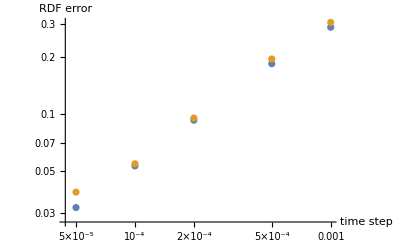

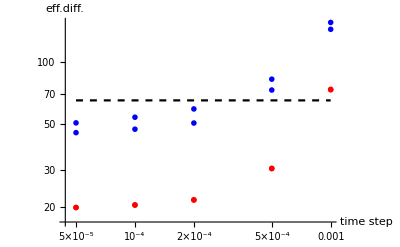

```mathematica
(* Summary of results. This is compiled by running Smoldyn many times and copying over the values. Each entry is time step and then result value. The suffixes m1 and m2 are for the bounce parameter. m1 is for bounce =-1 and m2 is for bounce -2. Saved as crowding3Ddiff.png *)
rdfsummarym1={{0.00005,0.032008},{0.0001,0.0531669},{0.0002,0.0928713},{0.0005,0.184951},{0.001,0.288626}}
rdfsummarym2={{0.00005,0.0386212},{0.0001,0.0545697},{0.0002,0.0953116},{0.0005,0.196007},{0.001,0.306062}}
diff2summarym1={{0.00005,19.7905},{0.0001,20.3138},{0.0002,21.4992},{0.0005,30.573},{0.001,73.4937}}
diff2summarym2={{0.00005,45.433},{0.0001,47.2023},{0.0002,50.5485},{0.0005,72.9132},{0.001,143.095}}
diff4summarym1={{0.00005,19.7825},{0.0001,20.383},{0.0002,21.5557},{0.0005,30.4636},{0.001,73.1084}}
diff4summarym2={{0.00005,50.6458},{0.0001,53.9205},{0.0002,59.118},{0.0005,82.26},{0.001,154.45}}
ListLogLogPlot[{rdfsummarym1,rdfsummarym2},AxesLabel->{"time\nstep","RDF error"}]
Show[{ListLogLogPlot[{diff2summarym1,diff2summarym2,diff4summarym1,diff4summarym2},AxesLabel->{"time\nstep","eff.diff."},PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]],Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]},PlotMarkers->{circle,circle,square,square},AxesStyle->Directive[Bold,12]],
LogLogPlot[65,{x,0.00005,0.001},PlotStyle->Directive[Black,Dashed]]}]
```